```mathematica
Clear@u;
input=3;
nNvec⟦input⟧
ν
aS = 3;
```

-7

13

```mathematica
h[u]=Sum[   wMatrix⟦aS,aQ⟧  Chop[Sum[bInMatrix[[aQ,xk+1,input]]u^(xk),{xk,0,Length[bMatrix]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify
h'[u]=D[h[u],{u,1}]
h''[u]=D[h[u],{u,2}]
hp2[u]=Sum[   wMatrix⟦aS,aQ⟧ Chop[Sum[bInMatrix[[aQ,xk+1,input+1]]u^(xk),{xk,0,Length[bMatrix]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify
hm2[u]=Sum[   wMatrix⟦aS,aQ⟧ Chop[Sum[bInMatrix[[aQ,xk+1,input-1]]u^(xk),{xk,0,Length[bMatrix]-1}]//N],{aQ,1,ns[J,K,ν]}]//FullSimplify
```

2.0383×10^-17+u (-1.73472×10^-18+u (-6.93889×10^-18+u (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))))))

-1.73472×10^-18+u (-6.93889×10^-18+u (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))))))+u (-6.93889×10^-18+u (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))))+u (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))))+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u)))))))

u (u (u (u (u (u ((2 (-13.9176-18.4262 u)-18.4262 u) u+2 (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u))+2 (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u)))+2 (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u))))+2 (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u)))))+2 (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u))))))+2 (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))))+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u)))))))+2 (-6.93889×10^-18+u (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))))+u (-0.35155+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))))+u (-2.18115+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))))+u (-2.29591+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)))+u (8.94709+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u))+u (21.0255+u (6.83543+(-13.9176-9.21312 u) u)+u (6.83543+(-13.9176-18.4262 u) u+(-13.9176-9.21312 u) u)))))))

2.35814×10^-17+u (3.03577×10^-17+u (4.03323×10^-17+u (0.350238+u (1.13359+u (-3.28873+u (-12.3795+u (0.267317+u (25.8581+(17.9556+0.209633 u) u))))))))

8.13152×10^-18+u (5.37764×10^-17+u (2.498×10^-16+u (0.179844+u (1.8793+u (7.1694+u (9.24067+u (-8.74672+u (-36.3732+(-35.6311-11.7845 u) u))))))))

```mathematica
Clear@n
f[u] = (1+u)^((ν+n)/4) (1-u)^((ν-n)/4) w[u];
FullSimplify[(-4/u) FullSimplify[D[FullSimplify[u*(1-u^2)D[f[u],{u,1}]],{u,1}]]]
```

-1/u(1-u)^(9/4-n/4) (1+u)^((9+n)/4) ((2 n+(-52+n^2) u-28 n u^2+221 u^3) w[u]+4 (-1+u^2) (-(1+(n-16 u) u) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[% +(f[u]/(1-u^2))*(ν^2+n^2-2ν n u) +(4f[u]/u^2)(1/2)(j(j+1)-n^2)-f[u]*k(k+4)]
```

1/u^2(1-u)^(13/4-n/4) (1+u)^((13+n)/4) ((2 j (1+j)-2 n^2-2 n u-(-13+k) (17+k) u^2) w[u]+4 u (-(1+(n-16 u) u) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[% +  (4/u^2) (1-u^2)^(1/2) (1/4)((j-n+2)(j-n+1)(j+n-1)(j+n))^(1/2)( (1+u)^((ν+n-2)/4) (1-u)^((ν-n+2)/4) wnm2[u])  +  (4/u^2) (1-u^2)^(1/2)  (1/4)((j-n)(j-n-1)(j+n+1)(j+n+2))^(1/2)( (1+u)^((ν+n+2)/4) (1-u)^((ν-n-2)/4) wnp2[u])]
```

1/u^2(1-u)^(13/4-n/4) (1+u)^((13+n)/4) ((2 j (1+j)-2 n^2-2 n u-(-13+k) (17+k) u^2) w[u]-√((1+j-n) (2+j-n) (-1+j+n) (j+n)) (-1+u) wnm2[u]+√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (1+u) wnp2[u]+4 u (-(1+(n-16 u) u) w'[u]+u (-1+u^2) w''[u]))

```mathematica
res=%
```

1/u^2(1-u)^(13/4-n/4) (1+u)^((13+n)/4) ((2 j (1+j)-2 n^2-2 n u-(-13+k) (17+k) u^2) w[u]-√((1+j-n) (2+j-n) (-1+j+n) (j+n)) (-1+u) wnm2[u]+√((-1+j-n) (j-n) (1+j+n) (2+j+n)) (1+u) wnp2[u]+4 u (-(1+(n-16 u) u) w'[u]+u (-1+u^2) w''[u]))

```mathematica
FullSimplify[res/.{j->J,k->K}]
```

1/u^2(1-u)^(13/4-n/4) (1+u)^((13+n)/4) (-2 (-132+n^2+n u+500 u^2) w[u]-√((-13+n) (-12+n) (10+n) (11+n)) (-1+u) wnm2[u]+√((-11+n) (-10+n) (12+n) (13+n)) (1+u) wnp2[u]+4 u (-(1+(n-16 u) u) w'[u]+u (-1+u^2) w''[u]))

```mathematica
%/.{n->nNvec⟦input⟧}
```

1/u^2(1-u)^5 (1+u)^(3/2) (-2 (-83-7 u+500 u^2) w[u]-4 √285 (-1+u) wnm2[u]+6 √255 (1+u) wnp2[u]+4 u (-(1+(-7-16 u) u) w'[u]+u (-1+u^2) w''[u]))

```mathematica
res3=FullSimplify[%/.{w[u]->h[u],w'[u]->h'[u],
w''[u]-> h''[u],
wnm2[u]-> hm2[u],wnp2[u]-> hp2[u]}]
```

-1/u^247.1381 (-1.+u)^5 √(1+u) (1.+u) (1.3136×10^-16+u (1.75116×10^-16+u (-3.15387×10^-17+u (2.22045×10^-16+u (1.77636×10^-15+u (-8.88178×10^-16+u (7.10543×10^-15-7.10543×10^-15 u+2.84217×10^-14 u^3-1.42109×10^-14 u^4-3.19744×10^-14 u^5)))))))

```mathematica
Chop[res3]
res3/.{u->1}
res3/.{u->0.5}
res3/.{u->0.01}
```

0.

0.

4.36875×10^-15

6.05669×10^-11

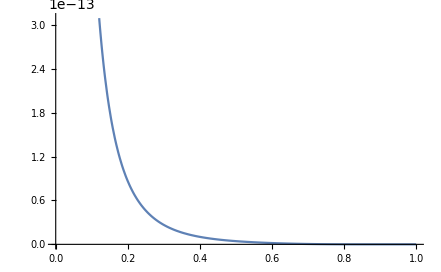

```mathematica
Plot[res3,{u,-.0000001,1}]
```